# Fast Flow Subsystem for B = ϵ^2 B0

```mathematica
ClearAll[ϕ,ψ,ψ0,A,B,B0,M,InvM,RHS,DynSis,phiPrime,psiPrime,APrime,BPrime,Da,Db,dA,dB,p,b,m,s,DynSis,DynSisV2,DynSisV3,DynSisV4,FastSlowEq];
F[A_,B_]:=-dA*A+m*B+2*p*A*B
G[A_,B_]:=B*(-dB-m-2*p*A+2*b-2*b*(A+B))
M[A_,B_]:={{Da*(1-B)+p*B,Da*A,0,0},{Db*B,Db*(1-A)-b*(A+B),0,0},{0,0,1,0},{0,0,0,1}}
(*Vector on the right-hand side*)
RHS[A_,B_]:={-s*ϕ-F[A,B],-s*ψ-G[A,B],ϕ,ψ};
(*order replacer*)
Da = ϵ;
Db = ϵ;
dA = ϵ^2;
dB = ϵ^2;
m = ϵ^3;
(*Inverted left-hand side matrix*)
InvM[A_,B_]:=Inverse[M[A,B]];
M[A,B] //MatrixForm;
InvM[A,B] //MatrixForm;
(*Isolating derivatives on the right hand-side {phiPrime,psiPrime,APrime,BPrime}*)
DynSis = FullSimplify[InvM[A,B].RHS[A,B]] 
(*Printing the Inverse Matrix on the Right and Side and the full simplified right hand side*)
Series[InvM,{ϵ,0,3}] //MatrixForm;
Series[DynSis,{ϵ,0,1}] //MatrixForm
```

{(A^2 (ϵ^3+b (-2 B p+2 B ϵ+ϵ^2))-(b B-ϵ) (B ϵ^3+s ϕ)-A (ϵ^3-B ϵ (2 p+ϵ^2)+b B (2 B (p-ϵ)+ϵ (2+(-1+ϵ) ϵ))+b s ϕ+s ϵ (ϕ+ψ)))/(b B (A+B) p-b (-1+B) (A+B) ϵ+(-1+A) B p ϵ+(-1+A+B) ϵ^2),(-2 b B (-1+A+B) (B (p-ϵ)+ϵ)+A B (-2 B p^2-2 p ϵ+ϵ^3)-B ϵ (ϵ (B p+ϵ+B (-1+p) ϵ+ϵ^2)+s ϕ)+s (B p+ϵ-B ϵ) ψ)/(b B (A+B) p-b (-1+B) (A+B) ϵ+(-1+A) B p ϵ+(-1+A+B) ϵ^2),ϕ,ψ}

((-2 A B p-s ϕ)/(B p)+((2 A^2 b B p+2 A^2 B^2 p^2+A b s ϕ+b B s ϕ-A b B s ϕ-b B^2 s ϕ-A B p s ψ) ϵ)/(b B^2 (A+B) p^2)+O[ϵ]^2
(2 b B-2 A b B-2 b B^2-2 A B p+s ψ)/(b (A+B))+((2 b B p-4 A b B p-2 b B^2 p-2 A B p^2+2 A^2 B p^2-A b s ϕ-b B s ϕ+p s ψ-A p s ψ) ϵ)/(b^2 (A+B)^2 p)+O[ϵ]^2
ϕ
ψ)

```mathematica
Eq:= DynSis == {0,0,0,0} 
equi:= Solve [Eq,{ϕ,ψ,A,B}]
NonTrivialEq = FullSimplify[equi[[2]]]
NonTrivialEq2 = FullSimplify[equi[[3]]]
Series[NonTrivialEq,{ϵ,0,1}];
(* Extract expressions for A and B *)
Aexpr = A /. NonTrivialEq;
Bexpr = B /. NonTrivialEq;
(* Expand in a series around ϵ = 0 *)
Series[Aexpr, {ϵ, 0, 2}]
Series[Bexpr, {ϵ, 0, 2}]
```

{ϕ→0,ψ→0,A→(-b ϵ^2 (1+ϵ)-p (-2 b+ϵ^2+2 ϵ^3)+√(-8 b^2 p ϵ^2+4 b p ϵ^4 (1+ϵ)+(p ϵ^2-b (2 p+ϵ^2+ϵ^3))^2))/(4 p (b+p)),B→-(p ϵ^2-b (2 p+ϵ^2+ϵ^3)+√(-8 b^2 p ϵ^2+4 b p ϵ^4 (1+ϵ)+(p ϵ^2-b (2 p+ϵ^2+ϵ^3))^2))/(4 b p)}

{ϕ→0,ψ→0,A→-(-2 b p+b ϵ^2+p ϵ^2+b ϵ^3+2 p ϵ^3+√(-8 b^2 p ϵ^2+4 b p ϵ^4 (1+ϵ)+(p ϵ^2-b (2 p+ϵ^2+ϵ^3))^2))/(4 p (b+p)),B→(-p ϵ^2+b (2 p+ϵ^2+ϵ^3)+√(-8 b^2 p ϵ^2+4 b p ϵ^4 (1+ϵ)+(p ϵ^2-b (2 p+ϵ^2+ϵ^3))^2))/(4 b p)}

(b p+√(b^2 p^2))/(2 p (b+p))-((b p+√(b^2 p^2)) ϵ^2)/(4 (b p^2))+O[ϵ]^3

(b p-√(b^2 p^2))/(2 b p)+((b-p+(√(b^2 p^2) (b+p))/(b p)) ϵ^2)/(4 b p)+O[ϵ]^3

## Insert B = ϵ^2 B0

```mathematica
B = (ϵ^2)*B0;
DynSisV2 = FullSimplify[InvM[A,B].RHS[A,B]];
Series[DynSisV2,{ϵ,0,1}] //MatrixForm
```

(-(s ϕ)/ϵ+(b B0 p s ϕ-s ψ)/b+((A^2 b^2-2 A^2 b^2 B0 p-A b^2 B0 s ϕ-A b^2 B0^2 p^2 s ϕ-s ψ+A s ψ+A b B0 p s ψ) ϵ)/(A b^2)+O[ϵ]^2
(s ψ)/(A b)-((-1+A) s ψ ϵ)/(A^2 b^2)+O[ϵ]^2
ϕ
ψ)

## 1st Attempt: ψ = ϵ * ψ0

```mathematica
ψ = ϵ * ψ0;
DynSisV3 =  FullSimplify[InvM[A,B].RHS[A,B]];
Series[DynSisV3,{ϵ,0,2}] //MatrixForm
(*We have to divide the right hand side at positions 2 and 4 by ϵ because of the derivative that also changes with the coordinate change*)
SimpDynSisV3 = FullSimplify[MapAt[#/(ϵ) &, DynSisV3, {{2} ,{4}}]];
(*Hide this line for not considering the epsilon on the left hand side*)
SimpDynSisV3 = FullSimplify[MapAt[# * ϵ &, SimpDynSisV3,{1}]];
Series[SimpDynSisV3,{ϵ,0,1}] //MatrixForm
```

(-(s ϕ)/ϵ+B0 p s ϕ+((A b-2 A b B0 p-b B0 s ϕ-b B0^2 p^2 s ϕ-s ψ0) ϵ)/b+((-2 A b^2 B0+2 A^2 b^2 B0+2 A^2 b B0 p-A^2 b^2 B0 p+2 A^2 b^2 B0^2 p^2+A b B0 s ϕ+2 A b^2 B0^2 p s ϕ+A b^2 B0^3 p^3 s ϕ-s ψ0+A s ψ0+A b B0 p s ψ0) ϵ^2)/(A b^2)+O[ϵ]^3
(s ψ0 ϵ)/(A b)+((2 A b^2 B0-2 A^2 b^2 B0-2 A^2 b B0 p-A b B0 s ϕ+s ψ0-A s ψ0) ϵ^2)/(A^2 b^2)+O[ϵ]^3
ϕ
ψ0 ϵ+O[ϵ]^3)

(-s ϕ+B0 p s ϕ ϵ+O[ϵ]^2
(s ψ0)/(A b)+((2 A b^2 B0-2 A^2 b^2 B0-2 A^2 b B0 p-A b B0 s ϕ+s ψ0-A s ψ0) ϵ)/(A^2 b^2)+O[ϵ]^2
ϕ
ψ0)

Here we get a (2-2) fast slow system, with ϕ and B0 being the fast variables.
The critical manifold would then be the set where [ϕ,ψ0]=[0,0], or in other words, when A and B would be constant as ϕ and ψ are the derivates of A and B, respectively.
We attempt then to compute the slow flow for this rescaling

```mathematica
(*The second line and third line would be representative of the slow flow*)
SlowFlowTEST = SimpDynSisV3[[{2,3}]] /. ϕ -> 0 /. ψ0 -> 0 
Series[SlowFlowTEST,{ϵ,0,1}] //MatrixForm
```

{(A B0 ϵ (2 p+2 B0 p^2 ϵ-ϵ^2)+2 b B0 ϵ (1+B0 (p-ϵ) ϵ) (-1+A+B0 ϵ^2)+B0 ϵ^3 (1+ϵ+B0 ϵ (p+(-1+p) ϵ)))/(-A (b+ϵ+b B0 (p-ϵ) ϵ+B0 p ϵ^2)+ϵ (-1+b B0 ϵ) (-1+B0 ϵ (-p+ϵ))),0}

(-((2 (-1+A) b B0+2 A B0 p) ϵ)/(A b)+O[ϵ]^2
0)

Analytically, this leads to a slow flow  (psi0, A) =  (0, 0) so the whole system is constant. We are not particularly interested on this type of effect.
We then move to the second attempt on replacing to a 1-3 fast slow system.

## 2nd Attempt: ψ = ϵ^2 ψ0

```mathematica
ψ = ϵ^2 * ψ0;
DynSisV4 = FullSimplify[InvM[A,B].RHS[A,B]];
Series[DynSisV4,{ϵ,0,3}];
(*We have to divide the right hand side at positions 2 and 4 by ϵ^2 because of the derivative that also changes with the coordinate change*)
SimpDynSisV4 = FullSimplify[MapAt[#/(ϵ^2) &, DynSisV4, {{2},{4}}]]
(*Hide this line for not considering the epsilon on the left hand side*)
Series[SimpDynSisV4,{ϵ,0,1}] //MatrixForm
```

{(-A^2 ϵ^2 (b+ϵ+2 b B0 (-p+ϵ))+ϵ (-1+b B0 ϵ) (B0 ϵ^5+s ϕ)+A (b B0 (-1+2 B0 p) ϵ^4+B0 (-1+b-2 b B0) ϵ^5+b s ϕ+s ϵ ϕ+ϵ^3 (1+2 b B0-2 B0 p+s ψ0)))/(ϵ (-A (b+ϵ+b B0 (p-ϵ) ϵ+B0 p ϵ^2)+ϵ (-1+b B0 ϵ) (-1+B0 ϵ (-p+ϵ)))),(A B0 (2 p+2 B0 p^2 ϵ-ϵ^2)+2 b B0 (1+B0 (p-ϵ) ϵ) (-1+A+B0 ϵ^2)+B0 ϵ^2 (1+ϵ+B0 ϵ (p+(-1+p) ϵ))+B0 s ϕ+s (-1+B0 ϵ (-p+ϵ)) ψ0)/(-A (b+ϵ+b B0 (p-ϵ) ϵ+B0 p ϵ^2)+ϵ (-1+b B0 ϵ) (-1+B0 ϵ (-p+ϵ))),ϕ,ψ0}

(-(s ϕ)/ϵ+B0 p s ϕ+(A-2 A B0 p-B0 s ϕ-B0^2 p^2 s ϕ) ϵ+O[ϵ]^2
-(2 (-1+A) b B0+2 A B0 p+B0 s ϕ-s ψ0)/(A b)+((2 b B0-4 A b B0+2 A^2 b B0-2 A B0 p+2 A^2 B0 p-B0 s ϕ+A B0 s ϕ+A b B0^2 p s ϕ+s ψ0-A s ψ0) ϵ)/(A^2 b^2)+O[ϵ]^2
ϕ
ψ0)

Here we get a (1-3) fast slow subsystem with ϕ being the fast variable
The critical manifold would then be the set where ϕ=0, or in other words, when A would be constant as ϕ is the derivates of A.

```mathematica
(*SimpDynSisV4 = FullSimplify[MapAt[# * ϵ &, SimpDynSisV4,{1}]]; We have to leave the ϵ in the first equation to the right hand side and therefore leave this line out)*)
FastSlowEq:= SimpDynSisV4 == {0,0,0,0}
FSEQ = Solve[FastSlowEq,{ϕ,ψ0,A,B0}]
(*Replace A and B0 with the equilibria*)
Aexpr = A /. FSEQ[[2]];
B0expr = B0/. FSEQ[[2]];
(* Expand in a series around ϵ = 0 *)
Series[Aexpr,{ϵ,0,2}]
Series[B0expr,{ϵ,0,2}]
```

{{ϕ→0,ψ0→0,A→0,B0→0},{ϕ→0,ψ0→0,A→(4 b-2 ϵ^2-(2 b ϵ^2)/p-4 ϵ^3-(2 b ϵ^3)/p+(√(-16 b p ϵ^2 (2 b-ϵ^2-ϵ^3)+(-4 b p-2 b ϵ^2+2 p ϵ^2-2 b ϵ^3)^2))/p)/(8 (b+p)),B0→(4 b p+2 b ϵ^2-2 p ϵ^2+2 b ϵ^3-√(-16 b p ϵ^2 (2 b-ϵ^2-ϵ^3)+(-4 b p-2 b ϵ^2+2 p ϵ^2-2 b ϵ^3)^2))/(8 b p ϵ^2)},{ϕ→0,ψ0→0,A→(4 b-2 ϵ^2-(2 b ϵ^2)/p-4 ϵ^3-(2 b ϵ^3)/p-(√(-16 b p ϵ^2 (2 b-ϵ^2-ϵ^3)+(-4 b p-2 b ϵ^2+2 p ϵ^2-2 b ϵ^3)^2))/p)/(8 (b+p)),B0→(4 b p+2 b ϵ^2-2 p ϵ^2+2 b ϵ^3+√(-16 b p ϵ^2 (2 b-ϵ^2-ϵ^3)+(-4 b p-2 b ϵ^2+2 p ϵ^2-2 b ϵ^3)^2))/(8 b p ϵ^2)}}

(b p+√(b^2 p^2))/(2 p (b+p))-((b p+√(b^2 p^2)) ϵ^2)/(4 (b p^2))+O[ϵ]^3

(b p-√(b^2 p^2))/(2 b p ϵ^2)+(2 b-2 p+(2 √(b^2 p^2) (b+p))/(b p))/(8 b p)+((b p-√(b^2 p^2)) ϵ)/(4 b p^2)+O[ϵ]^3

## Eigenvalues and Eigenvectors for 2 first equilibria (trivial and nontrivial)

```mathematica
(*FullParameter = {ϵ -> 0.1, p -> 0.2, s -> 0.2, b -> 0.04};*)
FullParameter = {ϵ -> 0.1, p -> 0.2, s -> 0.2, b -> 0.16};
JacFSEQ = FullSimplify[D[SimpDynSisV4,{{ϕ,ψ0,A,B0}}]];
(*For the trivial equilibrium*)
JacTrivialFSEQ = JacFSEQ /. FSEQ[[1]] /. {ϵ->0.1, p->0.2};
eigenTrivial[b_,s_] = Eigenvalues[JacTrivialFSEQ];
NumJacTrivialFSEQ = JacFSEQ /. FSEQ[[1]] /. FullParameter;
NumJacTrivialFSEQEigenvalues = Eigenvalues[NumJacTrivialFSEQ];
(*For the first nontrivial equilibrium*)
JacNonTrivial1FSEQ = JacFSEQ /. FSEQ[[2]] /.{ϵ->0.1, p->0.2};
eigenNonTrivial[b_,s_] = Eigenvalues[JacNonTrivial1FSEQ];
(*eigenvecNontrivial[b_, s_] := Eigenvectors[JacNonTrivial1FSEQ];*)
(*Get the series expansion fot eigenvalues and eigenvectors on b and s*)
FullSimplify[Series[eigenNonTrivial[b,s],{b,0.16,0},{s,0.2,0}]]
(*FullSimplify[Series[eigenvecNontrivial[b,s],{b,0.16,0},{s,0.2,0}]];*)
(*For full parameter replacement including b and s*)
NumJacNonTrivial1FSEQ = JacNonTrivial1FSEQ /. FullParameter
NumJacNonTrivial1FSEQEigenvalues = Eigenvalues[NumJacNonTrivial1FSEQ] //MatrixForm
eigenNonTrivial[0.16,0.2][[2]]
```

Root::sbr: Because of branch cuts, the series may represent a different root of (1.15162×10^6 b^4)/((0.0000348472-0.0210579 b+0.0607263 b^2+«1»+«21» √(«1»)-0.0803055 b √Plus[«3»]-0.412882 b^2 √Plus[«3»])^4)-(5.5434×10^9 b^5)/(0.0000348472-0.0210579 b+«7»)^4+(1.22867×10^13 b^6)/(«1»)^4-(1.6603×10^16 b^7)/(«1»)^4+(«23» b^8)/(«1»)^4-(«23» «1»)/(«1»)^4+«56»+(«1»)/(«1»)-(«22» b^9 √(«1»))/(«1»)^4+(8.57129×10^26 b^(«2») √(«24»-«21» b+0.611684 b^2))/(«1»)^4-(2.82491×10^29 b^11 √(0.000016-0.006224 b+0.611684 b^2))/(«1»)^4+(6.80828×10^31 b^12 √(0.000016-0.006224 b+0.611684 b^2))/(«1»)^4+«35»& for some values of {s,b}.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

{(-1.98061+O[s-0.2]^1)+O[b-0.16]^1,(14.6994+O[s-0.2]^1)+O[b-0.16]^1,((0.0354071-0.266734 ⅈ)+O[s-0.2]^1)+O[b-0.16]^1,((0.0354071+0.266734 ⅈ)+O[s-0.2]^1)+O[b-0.16]^1}

{{-1.8071,-0.059552,0.533319,-0.0128342},{-35.3952,14.5967,-130.579,-0.878157},{1,0,0,0},{0,1,0,0}}

(14.6994+0. ⅈ
-1.98114+0. ⅈ
0.0356703+0.268993 ⅈ
0.0356703-0.268993 ⅈ)

14.6994

## Eigenvalues of the trivial equilibria of the rescaled system plotted

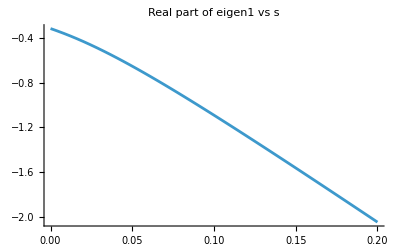

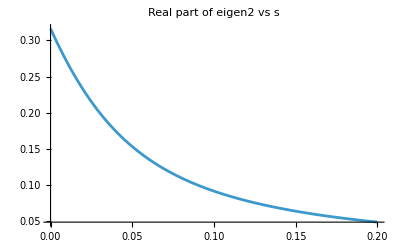

-Graphics3D-

-Graphics3D-

```mathematica
Plot[Re[eigenTrivial[b,s][[1]]],{s,0,0.2},PlotLabel->"Real part of eigen1 vs s"]
Plot[Re[eigenTrivial[b,s][[2]]],{s,0,0.2},PlotLabel->"Real part of eigen2 vs s"]
Plot3D[
 Re[eigenTrivial[b,s][[3]]],
{b,  0.01, 0.16}, {s, 0.01, 0.2},
 PlotLabel -> "Real part of eigen3 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen3]"},
 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]

Plot3D[
 Re[eigenTrivial[b,s][[4]]],
{b,  0.01, 0.16}, {s, 0.01, 0.2},
 PlotLabel -> "Real part of eigen4 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen4]"},
 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
```

# Eigenvalues of the first non trivial equilibrium of the rescaled system plotted

```mathematica
Plot3D[
 Re[eigenNonTrivial[b_,s_][[1]]],
 {b,  0.01, 0.16}, {s, 0.01, 0.2},
 PlotLabel -> "Real part of Eigenvalue 1 vs b and s", 
 AxesLabel -> {"b", "s", "Re[eigen1]"}, 

 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}},
 (* Ensure full z-range is displayed *)
 PlotRange -> All, 
 Ticks -> {Automatic, Automatic, Automatic}
]
Plot3D[
 Re[eigenNonTrivial[b_,s_][[2]]],
 {b,  0.01, 0.16}, {s, 0.01, 0.2},
 PlotLabel -> "Real part of Eigenvalue 2 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen2]"},

 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}},
 
 (* Ensure full z-range is displayed *)
 PlotRange -> All, 
 Ticks -> {Automatic, Automatic, Automatic}
]
Plot3D[
 Re[eigenNonTrivial[b_,s_][[3]]],
{b,  0.01, 0.16}, {s, 0.01, 0.2},
 PlotLabel -> "Real part of Eigenvalue 3 vs b and s", 
 AxesLabel -> {"b", "s", "Re[eigen3]"},

 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}},
 
 (* Ensure full z-range is displayed *)
 PlotRange -> All, 
 Ticks -> {Automatic, Automatic, Automatic}
]
Plot3D[
 Re[eigenNonTrivial[b_,s_][[4]]],
 {b,  0.01, 0.16}, {s, 0.01, 0.2},
 PlotLabel -> "Real part of Eigenvalue 4 vs b and s", 
 AxesLabel -> {"b", "s", "Re[eigen4]"}, 
 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}},
 
 (* Ensure full z-range is displayed *)
 PlotRange -> All, 
 Ticks -> {Automatic, Automatic, Automatic}
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

## Slow flow system calculation

```mathematica
(*ϕ = 0 represents the slow flow. We then plug it in the (1-3) fast-slow system SimpDynSisV4*)
SlowFlow = SimpDynSisV4[[{2,3,4}]] /. ϕ -> 0 
Series[SlowFlow,{ϵ,0,1}] //MatrixForm
```

{(A B0 (2 p+2 B0 p^2 ϵ-ϵ^2)+2 b B0 (1+B0 (p-ϵ) ϵ) (-1+A+B0 ϵ^2)+B0 ϵ^2 (1+ϵ+B0 ϵ (p+(-1+p) ϵ))+s (-1+B0 ϵ (-p+ϵ)) ψ0)/(-A (b+ϵ+b B0 (p-ϵ) ϵ+B0 p ϵ^2)+ϵ (-1+b B0 ϵ) (-1+B0 ϵ (-p+ϵ))),0,ψ0}

(-(2 (-1+A) b B0+2 A B0 p-s ψ0)/(A b)+((2 b B0-4 A b B0+2 A^2 b B0-2 A B0 p+2 A^2 B0 p+s ψ0-A s ψ0) ϵ)/(A^2 b^2)+O[ϵ]^2
0
ψ0)

Is the